# https : // doi . org/10.1016/S0146 - 6410 (03) 90015 - 9

```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
XXXWWW=GaussianQuadratureWeights[5,0,1];
```

```mathematica
Integauss1d[f_,xc_:1]:=Module[{f1,f2},
f1[x_]:=f[xc*x];
f2[x_]:=1/x^2*f[xc/x];
xc*Sum[XXXWWW[[i,2]]*(f1[XXXWWW[[i,1]]]+f2[XXXWWW[[i,1]]]),{i,1,Length[XXXWWW]}]
]
```

```mathematica
Integrate1d[f_,xc_:1]:=Module[{f1,f2},
f1[x_]:=f[xc*x];
f2[x_]:=1/x^2*f[xc/x];
xc*NIntegrate[f1[x]+f2[x],{x,0,1}]
]
```

```mathematica
NIntegrate[ⅇ^(-x^2),{x,0,∞}]//Timing
```

{0.004479,0.886227}

```mathematica
Integrate1d[Function[x,ⅇ^(-x^2)]]//Timing
```

{0.005772,0.886227}

```mathematica
Integauss1d[Function[x,ⅇ^(-x^2)]]//Timing
```

{0.000166,0.885664}

```mathematica
For[i=0,i<10^5,i++,Integrate1d[Function[x,ⅇ^(-x^2)]]]
```

$Aborted

```mathematica
For[i=0,i<10^5,i++,Integrate1d[Function[x,ⅇ^(-x^2)]]]
```

## Constants

```mathematica
hbar=0.1973269804;
```

## Tesing gaussian expansion

```mathematica
Nfunc[νn_,l_]:=√((2^(l+2)*(2*νn)^(l+3/2))/(√π*Factorial2[2*l+1]))
```

```mathematica
ϕfunc[r_,νn_,l_]:=Nfunc[νn,l]*r^l*ⅇ^(-νn*r^2)
```

```mathematica
intesphericalharmonicradial[νn_,l_]:=Integrate[r^2*Conjugate[ϕfunc[r,νn,l]]*ϕfunc[r,νn,l],{r,0,∞}]
```

```mathematica
Table[intesphericalharmonicradial[1,i],{i,0,5}]
```

{1,1,1,1,1,1}

```mathematica
intesphericalharmonicangular[l_,m_]:=Integrate[Sin[θ]*Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]*SphericalHarmonicY[l,m,θ,ϕ],{θ,0,π},{ϕ,0,2π}]
```

```mathematica
Table[intesphericalharmonicangular[i,0],{i,0,5},{j,0,i}]
```

{{1},{1,1},{1,1,1},{1,1,1,1},{1,1,1,1,1},{1,1,1,1,1,1}}

### Testing <G_nl^G|G_(n-1l)^G> independece of n

```mathematica
gaussianoverlap[l_,n_:0,r1_:2,a_:3]:=Integrate[r^2*Conjugate[ϕfunc[r,1/(r1^2*a^(2n-2)),l]]*ϕfunc[r,1/(r1^2*a^(2n-4)),l],{r,0,∞}]
```

```mathematica
Table[Table[gaussianoverlap[l,n],{n,0,l}],{l,0,5}]
```

{{(3 √(3/5))/5},{(9 √(3/5))/25,(9 √(3/5))/25},{(27 √(3/5))/125,(27 √(3/5))/125,(27 √(3/5))/125},{(81 √(3/5))/625,(81 √(3/5))/625,(81 √(3/5))/625,(81 √(3/5))/625},{(243 √(3/5))/3125,(243 √(3/5))/3125,(243 √(3/5))/3125,(243 √(3/5))/3125,(243 √(3/5))/3125},{(729 √(3/5))/15625,(729 √(3/5))/15625,(729 √(3/5))/15625,(729 √(3/5))/15625,(729 √(3/5))/15625,(729 √(3/5))/15625}}

### DiagonalMatrix stuff in gaussian basises

```mathematica
NMatfunc[νn1_,νn2_,l_]:=((2 √(νn1*νn2))/(νn1+νn2))^(l+3/2);
TMatfunc[νn1_,νn2_,l_,μ_,hbar_]:=hbar^2/μ*((2*l+3)*νn1*νn2)/(νn1+νn2)*((2 √(νn1*νn2))/(νn1+νn2))^(l+3/2);
(*VMatfunc[νn1_,νn2_,V_,l_]:=Nfunc[νn1,l]*Nfunc[νn2,l]*NIntegrate[r^(2*l)*ⅇ^(-(νn1+νn2)*r^2)*V[r]*r^2,{r,0,∞}]*)
VMatfunc[νn1_,νn2_,V_,l_]:=Nfunc[νn1,l]*Nfunc[νn2,l]*Quiet[Integauss1d[Function[r,r^(2*l)*ⅇ^(-(νn1+νn2)*r^2)*V[r]*r^2]]];
```

```mathematica
VMatfuncsq[νn1_,νn2_,l_]:=(l+3/2)/(νn1+νn2)*((2 √(νn1*νn2))/(νn1+νn2))^(l+3/2);
VMatfunccolumb[νn1_,νn2_,l_]:=2/(√π)*(2^l*Factorial[l])/Factorial2[2*l+1] √(νn1+νn2)*((2 √(νn1*νn2))/(νn1+νn2))^(l+3/2);
VMatfuncexp[νn1_,νn2_,l_,μ_]:=((2 √(νn1*νn2))/(νn1+νn2+μ))^(l+3/2);
```

```mathematica
Module[{tmpf},
tmpf[r_]:=r^2;
VMatfunc[3/4,3/2,tmpf,0]//Simplify
]
```

0.610301

```mathematica
VMatfuncsq[3/4,3/2,0]//N
```

0.610301

```mathematica
νnf[n_,r1_,rmax_,nmax_]:=1/r1^2*(r1/rmax)^((2*n-2)/(nmax-1))
```

## Examples

### deuteron

#### gaussian expansion method

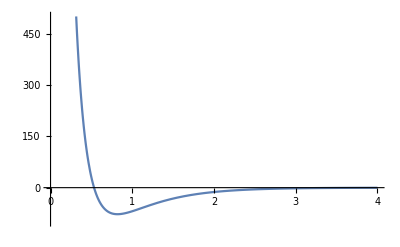

```mathematica
Vdeuteron[r_]:=(-626.885 ⅇ^(-1.55*r)+1438.72*ⅇ^(-3.11*r))/r
Plot[Vdeuteron[r],{r,0,4},PlotRange->{-100,500}]
```

```mathematica
ndeu=30;
```

```mathematica
νntdeuteron=Table[νnf[i,0.1,30,30],{i,1,30}];
```

```mathematica
VMatdeuteron=Table[VMatfunc[νntdeuteron[[i]],νntdeuteron[[j]],Vdeuteron,0],{i,1,30},{j,1,30}];
```

```mathematica
TMatdeuteron=Table[TMatfunc[νntdeuteron[[i]],νntdeuteron[[j]],0,1.0,√(2*41.47)],{i,1,30},{j,1,30}];
```

```mathematica
NMatdeuteron=Table[NMatfunc[νntdeuteron[[i]],νntdeuteron[[j]],0],{i,1,30},{j,1,30}];
```

```mathematica
{EigvalsDeuteron,EigvecsDeuteron}=Eigensystem[{TMatdeuteron+VMatdeuteron,NMatdeuteron},30];
```

```mathematica
EigvalsDeuteron
```

{87689.5,48050.6,31081.9,19462.7,12516.6,8168.42,5651.77,3914.51,2598.86,1714.45,1145.16,748.864,500.865,330.969,214.4,141.685,93.6602,61.5425,40.1438,26.0714,16.9158,10.8816,6.93192,4.31901,2.6079,-2.44438,1.48467,0.763531,0.317986,0.076567}

```mathematica
EigvalsDeuteron[[26]]
EigvecsDeuteron[[26]]
```

-2.44438

{-0.000251279,0.00215018,-0.00701511,0.01435,-0.0240772,0.0370868,-0.0500074,0.0544255,-0.0380177,-0.00826362,0.0872896,-0.17681,0.247416,-0.284291,0.296368,-0.308477,0.307801,-0.309132,0.296695,-0.289734,0.26906,-0.252779,0.222362,-0.192811,0.1522,-0.111199,0.0693286,-0.0348924,0.0122872,-0.00223153}

```mathematica
WavefunctionDeuteron[r_]:=Sum[EigvecsDeuteron[[26,i]]*ϕfunc[r,νntdeuteron[[i]],0],{i,1,30}]
```

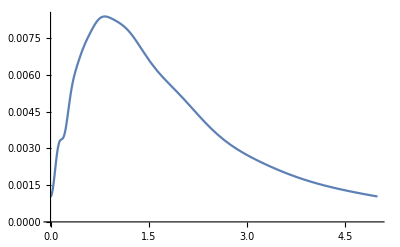

```mathematica
Plot[-WavefunctionDeuteron[x],{x,0.0,5.0}]
```

### □^4 he

#### gaussian expansion method

```mathematica
Nhe4=60;
```

```mathematica
potentialhe4[r_]:=Module[{rm=2.9673,ϵ=10.8,A=0.5448504*^6,α=13.353384,C6=1.3732412,C8=0.4253785,C10=0.178100,D=1.241314,x,F},
x=r/rm;
F[x]:=If[x<D,ⅇ^(-(D/x-1)^2),1];
ϵ*(A*ⅇ^(-α*x)-(C6/x^6+C8/x^8+C10/x^10)*F[x])
]
```

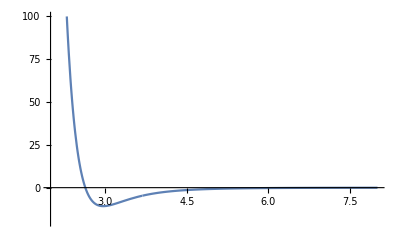

```mathematica
Plot[potentialhe4[x],{x,2.0,8.0},PlotRange->{-20,100}]
```

```mathematica
νnthe4=Table[νnf[i,0.14,700.0,Nhe4],{i,1,Nhe4}];
```

```mathematica
VMathe4=Table[Quiet[VMatfunc[νnthe4[[i]],νnthe4[[j]],potentialhe4,0]],{i,1,Nhe4},{j,1,Nhe4}];
```

```mathematica
TMathe4=Table[TMatfunc[νnthe4[[i]],νnthe4[[j]],0,1.0,√(2*12.119303326402733)],{i,1,Nhe4},{j,1,Nhe4}];
```

```mathematica
NMathe4=Table[NMatfunc[νnthe4[[i]],νnthe4[[j]],0],{i,1,Nhe4},{j,1,Nhe4}];
```

```mathematica
{Eigvalshe4,Eigvecshe4}=Eigensystem[{TMathe4+VMathe4,NMathe4},Nhe4];
```

```mathematica
Eigvalshe4
```

{9.25909×10^6,5.53943×10^6,1.76281×10^6,320252.,79530.8,35400.2,21122.4,8109.3,4994.07,4060.17,2357.46,2047.85,1770.52,996.596,412.308,267.077,243.516,149.299,101.385,67.75,46.3625,33.0309,24.1502,17.2257,12.2894,8.7444,6.28541,4.52109,3.27999,2.3785,1.73764,1.26739,0.930638,0.682116,0.502647,-0.3867,0.369814,0.273165,0.201586,0.14915,0.110318,0.081721,0.0605328,0.0448642,0.0332392,0.0246152,0.018206,0.013439,0.00988957,0.00724411,0.00527131,0.00379939,0.00270158,0.0018835,0.00127575,0.000827126,0.00050059,0.000269684,0.00011625,0.0000285371}

```mathematica
Wavefunctionhe4[r_]:=Sum[Eigvecshe4[[56,i]]*ϕfunc[r,νnthe4[[i]],0],{i,1,Nhe4}]
```

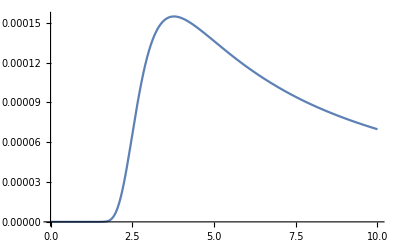

```mathematica
Plot[-Wavefunctionhe4[x],{x,0.0,10.0}]
```

## Testing